## Block’s stuff

## Wall’s stuff

## Problem’s stuff

## Testing

```mathematica
(*Properties initialization*)
nelx=30;nely=20;b=2;h=1;P=0.1;μ=0.7;
setProblemProperties[nelx,nely,b,h,P,μ];
```

```mathematica
(*Contacts generation*)
generateContacts[];
```

```mathematica
(*Loads*)
p=Table[{0,0,0,0,0,0},{nelx}];
p[[10]]={0,0,20,8.,0,0};
(*p[[3]]={0,0,10,-5,0,0};
p[[5]]={0,0,10,10,0,0};
p[[6]]={0,0,10,-35,0,0};*)
p=Flatten[p];
setBoundaryConditions[p];
```

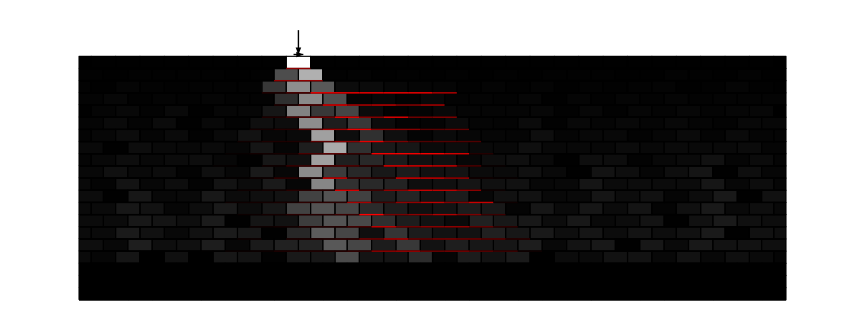

```mathematica
(*Solution*)
solveProblem[]
```

```mathematica
eqCheck
```

False

```mathematica
checkBlockEquilibrium[{nRow_,j_}]:=Module[{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb,Vtot,Htot,Mtot},
{Lsu,Vsu,Lsb,Vsb,Ns,Ts,Nc,Tc,Nd,Td,Rs,Vs,Rc,Vc,Rd,Vd,Ldu,Vdu,Ldb,Vdb}=getBlockLoads[{nRow,j}];

If[isBlockHalved[{nRow,j}],
Vtot=Vsu+Vsb+Ns+Nc+P/2+Nd-Vdu-Vdb-Rs-Rc-Rd;
Htot=Lsu+Lsb+Ts+Tc+Td-Ldu-Ldb-Vs-Vc-Vd;
If[isBlockOnLeftEdge[{nRow,j}],
Mtot=(Ns-Rs+Vsu+Vsb-Nd+Rd+Vdu+Vdb-P/2/2)b/2-h(Lsu-Ldu+Ts+Tc+Td);,
Mtot=(Ns-Rs+Vsu+Vsb-Nd+Rd+Vdu+Vdb+P/2/2)b/2-h(Lsu-Ldu+Ts+Tc+Td);
];,
Vtot=Vsu+Vsb+Ns+Nc+P+Nd-Vdu-Vdb-Rs-Rc-Rd;
Htot=Lsu+Lsb+Ts+Tc+Td-Ldu-Ldb-Vs-Vc-Vd;
Mtot=(Ns-Rs+Vsu+Vsb-Nd+Rd+Vdu+Vdb)b/2-h(Lsu-Ldu+Ts+Tc+Td);
];

{Vtot,Htot,Mtot}
];
```

```mathematica
c={};
For[nRow=1,nRow≤nely,nRow++,
For[j=1,j≤getTotalBlocksInRow[nRow],j++,
If[Chop[checkBlockEquilibrium[{nRow,j}],10^-3]≠{0,0,0},
AppendTo[c,{nRow,j}];
];
];
];
c
```

{{16,1},{16,2},{16,3},{16,4},{16,5},{16,6},{16,7},{16,8},{16,9},{16,10},{16,11},{16,12},{16,13},{16,14},{16,15},{16,16},{16,17},{16,18},{16,19},{17,1},{17,2},{17,3},{17,4},{17,5},{17,6},{17,7},{17,8},{17,9},{17,10},{17,11},{17,12},{17,13},{17,14},{17,15},{17,16},{17,17},{17,18},{17,19},{17,20},{18,1},{18,2},{18,3},{18,4},{18,5},{18,6},{18,7},{18,8},{18,9},{18,10},{18,11},{18,12},{18,13},{18,14},{18,15},{18,16},{18,17},{18,18},{18,19},{19,1},{19,2},{19,3},{19,4},{19,5},{19,6},{19,7},{19,8},{19,9},{19,10},{19,11},{19,12},{19,13},{19,14},{19,15},{19,16},{19,17},{19,18},{19,19},{19,20},{20,1},{20,2},{20,3},{20,4},{20,5},{20,6},{20,7},{20,8},{20,9},{20,10},{20,11},{20,12},{20,13},{20,14},{20,15},{20,16},{20,17},{20,18},{20,19}}

```mathematica
r=15;
```

```mathematica
getBlockLoads[{r,getTotalBlocksInRow[r]}]
```

{0,0,0,0,0,0,0.951497,0.0269494,0,0,0,0,1.0015,0.0269494,0,0,0.00194941,0,0.025,0}

```mathematica
solveHalvedBlockL2R[getBlockLoads[{r,getTotalBlocksInRow[r]}],False]
```

{0,0,0,0,0,0,0.951497,0.0269494,0,0,0,0.,1.0015,0.025,0,0,0.00194941,0,0.,0}

```mathematica
contacts[[getBlockNum[{14,19}]]]
```

1

```mathematica
checkBlockEquilibrium[{15,20}]
```

{0.,-0.0269494,0.}

```mathematica
applyLoads[]
```

```mathematica
nRow=6;
```

```mathematica
solveRow[19]
```

$Aborted

```mathematica
transferContactActionsBelow[18]
```

```mathematica
blockSequence=findSolvableBlockSequence[nRow];
```

```mathematica
blockSequence["seq"][[2]]
```

{8,9,10,11,12,13,14,15,16,17,18,19}

```mathematica
For[j=1,j<=Length[blockSequence["seq"]],j++,
Do[
blockLoads=getBlockLoads[{nRow,k}];
contact=contacts[[getBlockNum[{nRow,k}]]];
blockLoads=solveBlock[blockLoads,contact,{nRow,k},blockSequence["dir"][[j]]];
updateStress[blockLoads,{nRow,k}];,
{k,blockSequence["seq"][[j]]}
];
];
```

```mathematica
σv[[getBlockNum[{6,10}]]]
```

{19707.3,217.789,330.287,3.65007,81.0778,24.6306,19517.9,238.331,633.713,7.73821,0,0.}

```mathematica
getBlockLoads[{6,10}]
```

{0,0,0,0,19707.3,217.789,330.287,3.65007,81.0778,24.6306,19517.9,238.331,633.713,7.73821,0,0.,0,0,0,0}

```mathematica
contacts[[getBlockNum[{6,10}]]]
```

3

```mathematica
solveBlock[getBlockLoads[{6,10}],3,{6,10},1]
```

{0,0,0,0,19707.3,217.789,330.287,3.65007,81.0778,24.6306,19517.9,238.331,633.713,7.73821,0,0.,0,0,0,0}

```mathematica
checkBlockEquilibrium[{6,10}]//Chop
```

{0,0,-5.65706×10^-10}

```mathematica
unbalancedBlocksData=checkRowEquilibrium[nRow,blockSequence["cri"]];
```

```mathematica
unbalancedBlocksData["eq_check"]
```

True

```mathematica
(*equilibrium checks*)
If[unbalancedBlocksData["eq_check"]&&Length[unbalancedBlocksData["blocks"]]!=0,
(*start correcting unbalanced blocks*)
rowEqCheck=startCorrectionWaves[nRow,unbalancedBlocksData];,
(*no block needs correction*)
rowEqCheck=unbalancedBlocksData["eq_check"];
];

rowEqCheck
```

True